```mathematica
Vykreslení řešení přes Explicitního Eulera vs přes automatick.08ou metodu v "NDSolve" 
g:=9.81
```

```mathematica
l:=1
θ:=2*Pi/3
time:={t,0,80}
```

```mathematica
s= NDSolve[{f''[t]+ (g/l)Sin[f[t]]==0,f[0]==θ,f'[0]==0},f,time]
```

{{f→InterpolatingFunction[…]}}

```mathematica
v= NDSolve[{y''[t] +(g/l)*Sin[y[t]]== 0, y[0] == θ, y'[0] == 0}, y, time,Method->"ExplicitEuler"]
```

{{y→InterpolatingFunction[{{0., 80.}}, <>]}}

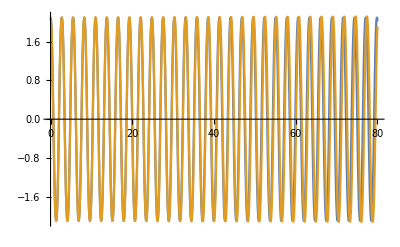

```mathematica
Plot[Evaluate[{f[t]/.s,y[t]/.v}],time,PlotRange->All]
```

```mathematica
Vykreslení závislosti energie na čase 
en =((y'[t])^2)/2-(g/l)Cos[y[t]]/.v
enpoc =-g/l *Cos[θ]
```

{-9.81 Cos[InterpolatingFunction[{{0., 80.}}, <>][t]]+1/2 (InterpolatingFunction[{{0., 80.}}, <>][t])^2}

4.905

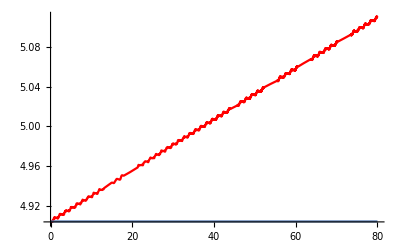

```mathematica
p1=Plot[Evaluate[{en}],time,PlotStyle->Red,PlotRange->All];
p2=Plot[Evaluate[{enpoc}],time,PlotRange->All];
Show[p1,p2,PlotRange->All]
```

StartingStepSize+a Eulera explicitního poli pro^2 Trajektorie ve vektorovém expl.Eulera

π/2

{{z[t]→InterpolatingFunction[{{0., 80.}}, <>][t],x[t]→InterpolatingFunction[{{0., 80.}}, <>][t]}}

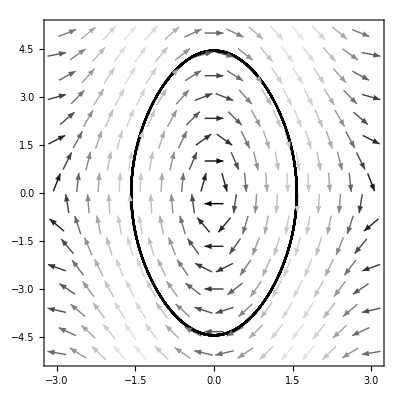

```mathematica
Trajektorie ve vektorovém poli pro explicitního Eulera a pro expl.Eulera + "StartingStepSize"
ϕ=Pi/2
eu=NDSolve[{x'[t] +(g/l)*Sin[z[t]]== 0,z'[t]==x[t], x[0] == 0, z[0] ==ϕ},{z[t],x[t]} , {t,0,80}, Method->"ExplicitEuler"]

field:=VectorPlot[{b, -g*Sin[a]/l}, {a, -3,3}, {b,-5,5}, PlotTheme->"Monochrome"];
line:=ParametricPlot[Evaluate[{z[t], x[t]} /. eu], {t, 0, 80}, PlotTheme->"Monochrome", PlotStyle->Thick];
Show[{field, line}]
```

```mathematica
sseu=NDSolve[{q'[t] +(g/l)*Sin[w[t]]== 0,w'[t]==q[t], q[0] == 0, w[0] == θ},{w[t],q[t]} , {t,0,120},StartingStepSize->1/99, Method->"ExplicitEuler"]
```

{{w[t]→InterpolatingFunction[…][t],q[t]→InterpolatingFunction[…][t]}}

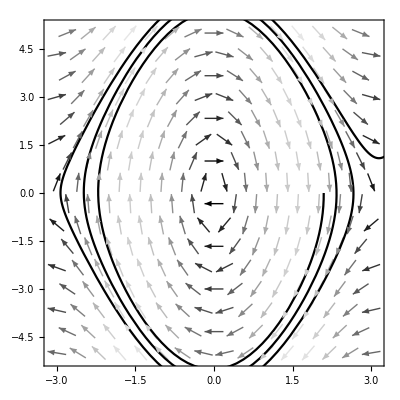

```mathematica
line2:=ParametricPlot[Evaluate[{w[t], q[t]} /. sseu], {t, 0, 80}, PlotTheme->"Monochrome"];
Show[{field, line2}]
```